# Vaje za 3. teden

6.  3.  2025

## Naloga 0

Napiši  funkcijo quickSort, ki sprejme seznam in vrne urejen seznam. Za urejanje naj uporabi algoritem quick sort

```mathematica
quickSort[seznam_]:=
If[Length[seznam]<= 1,seznam,
Module[{seznamManjsi,seznamEnaki,seznamVecji},
seznamManjsi=Select[seznam,#<First[seznam] &];
seznamEnaki=Select[seznam,#==First[seznam]&];
seznamVecji=Select[seznam,#>First[seznam]&];
Join[quickSort[seznamManjsi],seznamEnaki,quickSort[seznamVecji]]
]
 (*Rekurzija*)
]
seznam={9,2,98,1000,3,4,2,1,-3};
quickSort[seznam]
```

{-3,1,2,2,3,4,9,98,1000}

## Naloga 1

Napišite prepisovalno pravilo, ki bo izračunalo produkt dvečlenika z dvočlenikom. S term pravilom oenostavi izraz (2x - 4)(3 - 4y).

```mathematica
prepDvoclenik={(a_+b_)(c_+d_)->a c + a d + b c + b d}; 
((2x)-4)(3-(4y))//.prepDvoclenik
```

-12+6 x+16 y-8 x y

## Naloga 2

a) Definiraj funkcijo nakljucnaStevila, ki sprejme naravno število n in vrne seznam naključnih celih števil med -100 in 100 dolžine n.
c) S  pomočjo  prepisovalnih  pravil implementiraj urejanje z mehurčki (Bubble sort).

```mathematica
NakljucnaStevila[n_]:=RandomInteger[{-100,100}, n]
prep={a___, b_, c_, d___} /; b>c -> {a,c,b,d}; (*a___ pomeni del seznama(ali 0), tako da to pomeni,
da algoritem zbira kos a dokler ne pride do elementov b in c, ki izpolnjujeta pogoj in na to seznam spremeni v obliko a, c, b ,d
torej se vrstni red menja. Pravilo se izvaj dokler se lahko -> torej dokler ni sortiran*)
NakljucnaStevila[10]//.prep
```

{-88,-86,-82,-43,-31,-31,-25,-25,18,36}

## Naloga 3

- Definiraj funkcijo ZadnjaStevka, ki kot argument sprejme naravno število n in vrne zadnjo števko števila n. (ZadnjaStevka(8138719) vrne 9)
- Definiraj funkcijo PrvaStevka, ki kot argument sprejme naravno število n in vrne prvo števko števila n. (PrvaStevka(8138719) vrne 8)
- Definiraj funkcijo Parabola, ki sprejme koeficiente parabole a, b in c in nariše graf parabole ax^2 + bx + c. Graf naj bo narisan tako, da bo teme parabole vedno vidno na sliki.

9

8

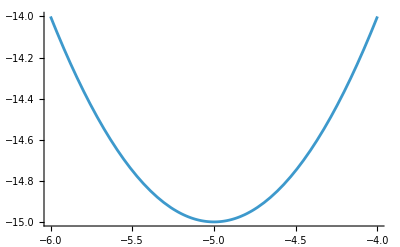

```mathematica
ClearAll[stev]
ZadnjaStevka[stev_]:=Mod[stev,10];
PrvaStevka[stev_]:=
Module[{s=stev},
While[s>=10,
s=Quotient[s,10]
];
s
]
stevilo=8138719;
ZadnjaStevka[stevilo]
PrvaStevka[stevilo]
Parabola[a_,b_,c_]:=Plot[a x^2+b x + c,{x,-b/2a-1,-b/2a +1}]
Parabola[1,10,10]
```

## Naloga 4

sesame naslednje sezname:
- {1/(2^20), 1/(2^19), ..., 1/2, 1, 2, 4, 8, ..., 2^24}
- {{}, {1}, {2}, {3}, ..., {99}, {99}, {98}, ..., {2}, {1}, {}}
- seznam dolžine 100, v katerem je vsak naslednji element za eno mesto bolj natančen približek števila π. ({3, 3.1, 3.14, ...})

```mathematica
Table[
1/Power[2,i],
{i,20,-25,-1}
];

F[j_]:={j}
Join[
{{}},
Table[F[j],{j,99}],
Table[F[j],{j,99,1,-1}],
{{}}
];
Join[{3},
Table[N[π,n],{n,2,100}]
];
```

## Naloga 5

Definiraj funkcijo, ki je za pozitivne x enaka sin(x)/x, za x manjši ali enak 0 pa je enaka cos(x). Pomagaj si s funkcijo `Piecewise`.

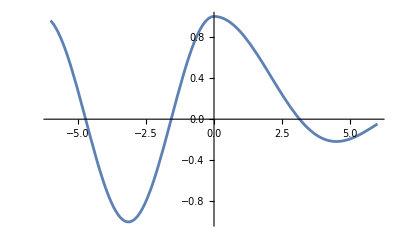

```mathematica
f[x_]:=Piecewise[{{Sin[x]/x,x>0}},Cos[x]]
Plot[f[x], {x,-6,6}]
```

## Naloga 6

Dano je zaporedje  
a) V Mathematici definiraj zaporedje .
b) Definiraj seznam, ki vrne prvih 30 členov zaporedja.
c) Izračunaj limito zaporedja . Izračunaj tudi limito zaporedja . Ali vrsta  konvergira?
d) Izračunaj numerični približek vsote vrste  (uporabi NSum).

```mathematica
A[n_]:=((2 n^2+n+1)/(2 n^2-1))^(-n^2)
prvih30=Table[A[i],3,{i,1,30}];
N/@ prvih30 (*to je isto, ko map*)
Limit[A[n],n->Infinity]
Limit[Power[A[n],1/n],n->Infinity]
NSum[A[n],{n,1,Infinity}]
```

{{0.25,0.163992,0.0982282,0.0589603,0.0354978,0.0214154,0.0129368,0.00782207,0.00473251,0.00286459,0.00173453,0.00105055,0.000636419,0.000385603,0.000233666,0.000141611,0.0000858304,0.0000520256,0.000031537,0.0000191183,0.0000115904,7.02691×10^-6,4.26037×10^-6,2.58312×10^-6,1.56622×10^-6,9.49668×10^-7,5.75839×10^-7,3.49172×10^-7,2.11731×10^-7,1.28392×10^-7},{0.25,0.163992,0.0982282,0.0589603,0.0354978,0.0214154,0.0129368,0.00782207,0.00473251,0.00286459,0.00173453,0.00105055,0.000636419,0.000385603,0.000233666,0.000141611,0.0000858304,0.0000520256,0.000031537,0.0000191183,0.0000115904,7.02691×10^-6,4.26037×10^-6,2.58312×10^-6,1.56622×10^-6,9.49668×10^-7,5.75839×10^-7,3.49172×10^-7,2.11731×10^-7,1.28392×10^-7},{0.25,0.163992,0.0982282,0.0589603,0.0354978,0.0214154,0.0129368,0.00782207,0.00473251,0.00286459,0.00173453,0.00105055,0.000636419,0.000385603,0.000233666,0.000141611,0.0000858304,0.0000520256,0.000031537,0.0000191183,0.0000115904,7.02691×10^-6,4.26037×10^-6,2.58312×10^-6,1.56622×10^-6,9.49668×10^-7,5.75839×10^-7,3.49172×10^-7,2.11731×10^-7,1.28392×10^-7}}

0

1/(√ⅇ)

0.660849

## Naloga 7

Dano  je  rekurzivno  zaporedje .

a) V Mathematici definiraj zaporedje  z začetnim členom .
b) Izračunaj prvih 5 členova zaporedja . Nato vse vse izraze razširi in združi na skupni ulomek.

```mathematica
a[1]:=b
a[n_]:=(1/6)*(a[n-1]^2+a[n-1]+6)

Seznam=Together[
Table[
a[i],
{i,1,5}
]//ExpandAll 
]
```

{b,1/6 (6+b+b^2),1/216 (288+18 b+19 b^2+2 b^3+b^4),(425088+14256 b+15372 b^2+2268 b^3+1225 b^4+112 b^5+42 b^6+4 b^7+b^8)/279936,1/470184984576(769882226688+16110876672 b+17575315200 b^2+3001380480 b^3+1685350800 b^4+231227136 b^5+93463272 b^6+14717880 b^7+4544065 b^8+616400 b^9+164332 b^10+23744 b^11+5110 b^12+560 b^13+100 b^14+8 b^15+b^16)}

## Naloga 8

Za zaporedje  z začetnima členoma  in  izračunajte njegovo limito. Uporabite RSolveValue.

```mathematica
ClearAll[a]
a[1]=0;
a[2]=1;
(*a[n_]:=a[n-1]+(n*a[n-2])/(n+1)*)
RSolveValue[{a[n+1]=a[n]+(n*a[n-1])/(n),a[1]=0,a[2]=1},a[Infinity],n]
```

RSolveValue::deqn: Equation or list of equations expected in the first argument.

RSolve::deqn: Equation or list of equations expected instead of a[-1+n]+a[n] in the first argument {a[-1+n]+a[n],0,1}.

RSolveValue[{a[-1+n]+a[n],0,1},a[∞],n]

## Naloga 9

Naslednje naloge reši s pomočjo vnosa z naravnim jezikom (brez znanja sintakse Mathematice in brez pomožnih računov). V vseh primerih se prepričaj, da je Mathematica razumela tvoj ukaz. Glej spodnji primer.

### Primer

Izračunaj 20. števko v decimalnem zapisu števila 1+1/2+1/3+...+1/100.

WolframAlphaQueryResults

### Naloge

Določi 443. števko v decimalnem zapisu števila pi.

```mathematica
StringTake[
ToString[
N[π,444]
],
-1
]
```

1

Izračunaj ploščino območja med krivuljama f(x)=3x^2+2x+1 in g(x)=4-4x^4.

```mathematica
Integrate[3 x^2+2 x +1,x]-Integrate[4-4 x^4,x]
```

-3 x+x^2+x^3+(4 x^5)/5

Izračunaj f(3), kjer je f(x)=1+1/x.

Izračunaj obseg elipse s polosema 4 in 3. Ugotovi približno vrednost.

Matej ima 512 jabolk, Jana pa 1024 jabolk. Koliko jabolk imata Matej in Jana skupaj?

Ali je 1009 praštevilo? Izračunaj vsoto 1/2+1/3+1/5+1/7+1/11+...+1/1009. Kaj predstavlja ta vsota?

## Naloga 10

Naslednje naloge reši z vnosom z naravnim jezikom.

### Naloge

Določi površino Slovenije in skupno dolžno njene meje.

Koliko Slovenij prekrije površino Rusije?

Kolikšna je temperatura sonca?